# Generic Natario warp drive and deflector shield

## Geometric quantities

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

### Geodesic equation checker

Compute the geodesic equations from a 4-velocity vector

```mathematica
ClearAll[geodesicEquations]
geodesicEquations[velU_,velL_]:=FullSimplify[
Table[
Sum[velU[[a]]D[velL[[b]],coordsU[[a]]],{a,1,4}]
-Sum[velU[[a]]Γ[[i,a,b]]velL[[i]],{i,1,4},{a,1,4}],
{b,1,4}
]
];
```

### Curvature tensors and energy density

```mathematica
ClearAll[RiemannLLLL];
RiemannLLLL=ParallelTable[
FullSimplify[
D[Γ[[i,j,l]],coordsU[[k]] ]-D[Γ[[i,j,k]],coordsU[[l]] ]+Sum[
Γ[[s,j,l]] Γ[[i,k,s]]-Γ[[s,j,k]] Γ[[i,l,s]],
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4},
{l,1,4}
];

ClearAll[RicciLL];
RicciLL=FullSimplify[ParallelTable[Sum[RiemannLLLL[[i,j,i,l]],{i,1,4}],{j,1,4},{l,1,4}] ];

ClearAll[RicciScalar];
RicciScalar=FullSimplify[Sum[gUU[[i,j]]RicciLL[[i,j]],{i,1,4},{j,1,4}] ];

ClearAll[EinsteinLL];
EinsteinLL=FullSimplify[RicciLL-(1/2)RicciScalar*gLL];

ClearAll[EnergyDensity];
EnergyDensity=FullSimplify[1/(8π)Sum[EinsteinLL[[a,b]]*nU[[a]]nU[[b]],{a,1,4},{b,1,4}]]
```

-1/(32 π α[t,x,y,z]^2)((vy^(0,0,0,1)[t,x,y,z]+vz^(0,0,1,0)[t,x,y,z])^2-4 vy^(0,0,1,0)[t,x,y,z] vx^(0,1,0,0)[t,x,y,z]-4 vz^(0,0,0,1)[t,x,y,z] (vy^(0,0,1,0)[t,x,y,z]+vx^(0,1,0,0)[t,x,y,z])+(vx^(0,0,1,0)[t,x,y,z]+vy^(0,1,0,0)[t,x,y,z])^2+(vx^(0,0,0,1)[t,x,y,z]+vz^(0,1,0,0)[t,x,y,z])^2)

## Vincent Geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

```mathematica
ClearAll[vincentPU]
vincentPU=energy(nU+Join[{0},VU]);

ClearAll[vincentNorm]
vincentNorm=FullSimplify[Solve[Sum[gLL[[a,b]]vincentPU[[a]]vincentPU[[b]],{a,1,4},{b,1,4}]==(-δ),energy]]
```

{{energy→-(√δ)/(√(1-velx^2-vely^2-velz^2))},{energy→(√δ)/(√(1-velx^2-vely^2-velz^2))}}

## Particle Hamiltonian

```mathematica
ClearAll[pL];
pL={pt,px,py,pz};

ClearAll[H];
H=FullSimplify[1/2Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]];

ClearAll[dHdpL];
dHdpL=FullSimplify[Table[D[H,pL[[i]]],{i,1,4}]];

ClearAll[dHdqU];
dHdqU=FullSimplify[Table[D[H,coordsU[[i]]],{i,1,4}]];

ClearAll[NormCons];
NormCons=Collect[Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]-δ,pt,FullSimplify];
```

## Transition functions

### Sharp

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x<=0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[CInfTransition];
CInfTransition[x_,a_,xa_,b_,xb_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;
CInfTransition[x_,y0_,x0_,Δx_]=FullSimplify[
CInfTransition[x,y0,x0,0,x0+Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

Piecewise[{{y0/(1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx)))), x>x0&&x<x0+Δx}, {0, x>x0}, {y0, True}}]

```mathematica
ClearAll[arg];
arg=Δx (1/(-x+x0)+1/(-x+x0+Δx));

FullSimplify[y0/(1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))))==(y0*Sech[arg])/(1+Tanh[arg]+Sech[arg])]

Limit[(y0*Sech[arg])/(1+Tanh[arg]+Sech[arg]),x->x0,Direction->"FromAbove"]

ClearAll[arg];
```

True

ConditionalExpression[y0, y0∈ℝ&&Δx>0]

```mathematica
FullSimplify[
Derivative[1,0,0,0][CInfTransition][x,y0,x0,Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

Piecewise[{{-(ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))) y0 Δx (1/(x-x0)^2+1/(-x+x0+Δx)^2))/((1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))))^2), x>x0&&x<x0+Δx}, {0, True}}]

This transformation is necessary, otherwise the exponentials blow up when computing this numerically

```mathematica
ExpToTrig[-(ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))) y0 Δx (1/(x-x0)^2+1/(-x+x0+Δx)^2))/((1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))))^2)]//FullSimplify
```

-(y0 Δx (2 (x-x0)^2+2 (-x+x0) Δx+Δx^2) Sech[1/2 Δx (1/(-x+x0)+1/(-x+x0+Δx))]^2)/(4 (x-x0)^2 (-x+x0+Δx)^2)

```mathematica
Limit[-(y0 Δx (2 (x-x0)^2+2 (-x+x0) Δx+Δx^2) Sech[1/2 Δx (1/(-x+x0)+1/(-x+x0+Δx))]^2)/(4 (x-x0)^2 (-x+x0+Δx)^2),x->x0,Direction->"FromAbove"]
```

ConditionalExpression[0, y0∈ℝ&&Δx>0]

### Alcubierre

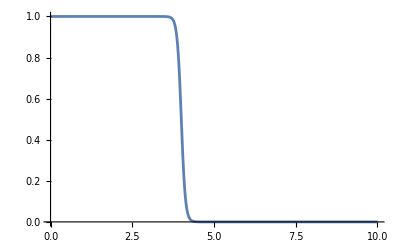

```mathematica
ClearAll[σ,R];
σ=8;
R=4;
Plot[(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ*R]),{r,0,10},PlotRange->Full]

ClearAll[σ,R];
```

```mathematica
D[(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ*R]),r]//FullSimplify
```

1/2 σ Coth[R σ] (-Sech[(r-R) σ]^2+Sech[(r+R) σ]^2)

### Polynomial

```mathematica
ClearAll[deg,poly];
deg=7;
poly[x_]=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==0,
Derivative[1][poly][x0]==0,
Derivative[1][poly][x0+dx]==0,
Derivative[2][poly][x0]==0,
Derivative[2][poly][x0+dx]==0,
Derivative[3][poly][x0]==0,
Derivative[3][poly][x0+dx]==0
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs];

ClearAll[polyTrans];
polyTrans[x_,y0_,x0_,dx_]=Piecewise[
{
{y0,x<x0},
{0,x>(x0+dx)},
{polyWithCs,True}
}
]

FullSimplify[Derivative[1,0,0,0][polyTrans][x,y0,x0,dx]]

StringReplace[ToString[polyWithCs,CForm],"powi"->"f64::powi"]
StringReplace[ToString[FullSimplify[D[polyWithCs,x]],CForm],"powi"->"f64::powi"]
```

Piecewise[{{y0, x<x0}, {0, x>dx+x0}, {((dx^3+4 dx^2 (x-x0)+10 dx (x-x0)^2+20 (x-x0)^3) (dx-x+x0)^4 y0)/dx^7, True}}]

Piecewise[{{0, x<x0||dx+x0<x}, {-(140 (x-x0)^3 (dx-x+x0)^3 y0)/dx^7, True}}]

((Power(dx,3) + 4*Power(dx,2)*(x - x0) + 10*dx*Power(x - x0,2) + 20*Power(x - x0,3))*Power(dx - x + x0,4)*y0)/Power(dx,7)

(-140*Power(x - x0,3)*Power(dx - x + x0,3)*y0)/Power(dx,7)

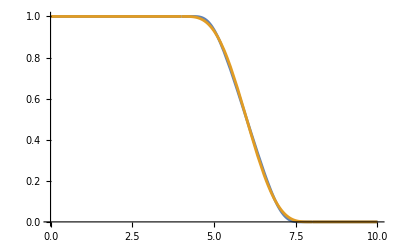

```mathematica
Plot[
{
Derivative[0,0,0,0][CInfTransition][x,1,4,4],
Derivative[0,0,0,0][polyTrans][x,1,4,4]
},
{x,0,10}
]
```

### Splines

```mathematica
ClearAll[order,midpointSlope,splineA,splineB]
order=6;
splineA[x_]=Sum[ca[i]x^i,{i,0,order}];
splineB[x_]=Sum[cb[i]x^i,{i,0,order}];

ClearAll[cas];
cas=Solve[
{
splineA[x0]==y0,
splineA[x0+dx/2]==y0/2,

Derivative[1][splineA][x0]==0,
Derivative[2][splineA][x0]==0,
Derivative[3][splineA][x0]==0,

Derivative[1][splineA][x0+dx/2]==-1/2,
Derivative[2][splineA][x0+dx/2]==0
},
Table[ca[i],{i,0,order}]
]//Flatten//FullSimplify;

ClearAll[cbs];
cbs=Solve[
{
splineB[x0+dx/2]==y0/2,
splineB[x0+dx]==0,

Derivative[1][splineB][x0+dx]==0,
Derivative[2][splineB][x0+dx]==0,
Derivative[3][splineB][x0+dx]==0,

Derivative[1][splineB][x0+dx/2]==-1/2,
Derivative[2][splineB][x0+dx/2]==0
},
Table[cb[i],{i,0,order}]
]//Flatten//FullSimplify;

ClearAll[SplineTrans];
SplineTrans[x_,y0_,x0_,dx_]=Piecewise[
{
{y0,x<=x0},
{0,x>=(x0+dx)},
{splineA[x]//.cas,x0<x<(x0+dx/2)},
{splineB[x]//.cbs,(x0+dx/2)<=x<(x0+dx)}
}
]//FullSimplify
```

Piecewise[{{y0, x≤x0}, {0, (dx+2 x0>2 x&&x≤x0)||dx+x0≤x}, {(20 dx^3 (x-x0)^4+dx^6 y0-320 (x-x0)^6 y0-24 dx^2 (x-x0)^4 (3 x-3 x0+5 y0)+64 dx (x-x0)^5 (x-x0+6 y0))/dx^6, x0<x<dx/2+x0}, {-(4 (dx-x+x0)^4 (3 dx^3-80 (x-x0)^2 y0-14 dx^2 (x-x0+y0)+16 dx (x-x0) (x-x0+4 y0)))/dx^6, True}}]

### Peter’s transition

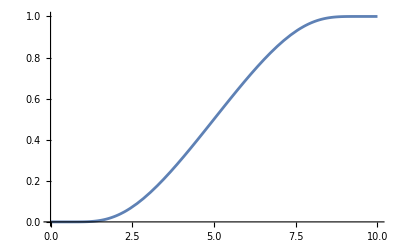

```mathematica
ClearAll[PeterTrans];
PeterTrans[x_,x0_,w_,q_,s_]:=1/2+1/2Tanh[s/π(Tan[π/(2w)(x-x0)]^2-q^2)/(Tan[π/(2w)(x-x0)])]

ClearAll[x0,w];
x0=0;
w=10;

Plot[PeterTrans[x,x0,w,1,2],{x,x0,w}]

ClearAll[x0,w];
```

```mathematica
FullSimplify[ExpandAll[TrigToExp[PeterTrans[x,x0,w,q,s]]]]
```

1/(1+ⅇ^((2 ⅈ (2 ⅇ^((ⅈ π (x+x0))/w) (-1+q^2)+(ⅇ^((2 ⅈ π x)/w)+ⅇ^((2 ⅈ π x0)/w)) (1+q^2)) s)/((ⅇ^((2 ⅈ π x)/w)-ⅇ^((2 ⅈ π x0)/w)) π)))

### Comparison

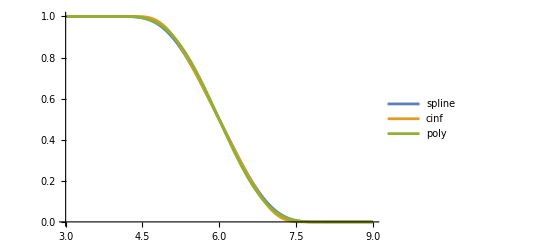

```mathematica
Plot[
{
SplineTrans[x,1,4,4],
CInfTransition[x,1,4,4],
polyTrans[x,1,4,4]
},
{x,3,9},
PlotLegends->{"spline","cinf","poly"}
]
```

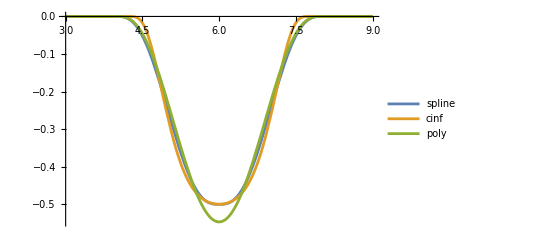

```mathematica
Plot[
{
Derivative[1,0,0,0][SplineTrans][x,1,4,4],
Derivative[1,0,0,0][CInfTransition][x,1,4,4],
Derivative[1,0,0,0][polyTrans][x,1,4,4]
},
{x,3,9},
PlotLegends->{"spline","cinf","poly"}
]
```

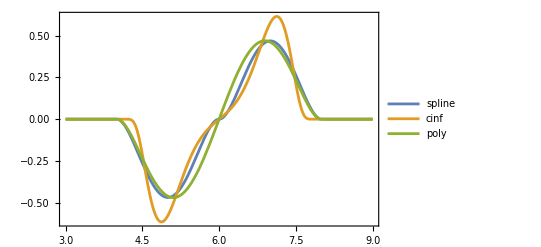

```mathematica
Plot[
{
Derivative[2,0,0,0][SplineTrans][x,1,4,4],
Derivative[2,0,0,0][CInfTransition][x,1,4,4],
Derivative[2,0,0,0][polyTrans][x,1,4,4]
},
{x,3,9},
PlotLegends->{"spline","cinf","poly"},
Axes->False,
Frame->True
]
```

### Adjusting the deflector position

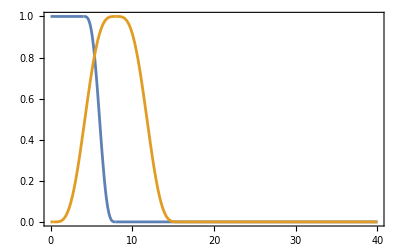

```mathematica
ClearAll[DeflectorPushout,DeflectorSigmaFactor,radius,sigma];
DeflectorPushout=1;
DeflectorSigmaFactor=19/10;
radius=4;
sigma=4;

Plot[
{
polyTrans[x,1,radius,sigma],
polyTrans[x-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]polyTrans[(radius+DeflectorPushout*sigma)-x,1,0,DeflectorSigmaFactor*sigma]
},
{x,0,40},
PlotRange->Full,
Axes->False,
Frame->True
]

ClearAll[pushout,sigmamult,radius,sigma];
ClearAll[DeflectorPushout,DeflectorSigmaFactor,radius,sigma];
```

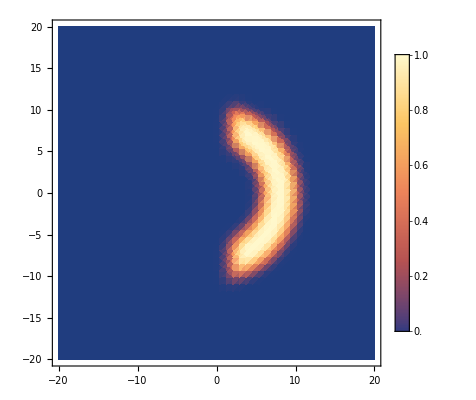

```mathematica
ClearAll[pushout,radius,sigma];
pushout=2;
radius=4;
sigma=4;

DensityPlot[
polyTrans[(radius+sigma)/2-x,1,0,sigma]polyTrans[Sqrt[x^2+y^2]-(radius+sigma),1,0,sigma]polyTrans[(radius+sigma)-Sqrt[x^2+y^2],1,0,sigma],
{x,-20,20},
{y,-20,20},
PlotRange->Full,
Exclusions->None,
PlotLegends->Automatic,
PlotPoints->50
]

ClearAll[pushout,radius,sigma];
```

## Code strings

### Proper formatting of Power

```mathematica
Unprotect[Power];
Format[Power[E,a_],CForm]:=(exp[a]);
Format[Power[a_,1/2],CForm]:=(sqrt[a]);
Format[Power[a_,-1/2],CForm]:=(1/sqrt[a]);
Format[Power[a_,3/2],CForm]:=(HoldForm[sqrt[a]^3]);
Format[Power[a_,b_],CForm]:=(powi[a,b])/;b∈Integers;
Format[Power[a_,b_],CForm]:=(powf[a,b]);
Protect[Power];
```

### Vincent equations RHS

```mathematica
ClearAll[rules];
rules={
vx[t,x,y,z]->lvx,
vy[t,x,y,z]->lvy,
vz[t,x,y,z]->lvz,

D[vx[t,x,y,z],x]->dvxdx,
D[vx[t,x,y,z],y]->dvxdy,
D[vx[t,x,y,z],z]->dvxdz,

D[vy[t,x,y,z],x]->dvydx,
D[vy[t,x,y,z],y]->dvydy,
D[vy[t,x,y,z],z]->dvydz,

D[vz[t,x,y,z],x]->dvzdx,
D[vz[t,x,y,z],y]->dvzdy,
D[vz[t,x,y,z],z]->dvzdz,

α[t,x,y,z]->lalp,

D[α[t,x,y,z],x]->dalpdx,
D[α[t,x,y,z],y]->dalpdy,
D[α[t,x,y,z],z]->dalpdz
};

ClearAll[stringRules];
stringRules={
"powi"->"f64::powi"
};

Print["let dx_dt = ",StringReplace[ToString[FullSimplify[dXudt[[1]]//.rules],CForm],stringRules],";\n"]

Print["let dy_dt = ",StringReplace[ToString[FullSimplify[dXudt[[2]]//.rules],CForm],stringRules],";\n"]

Print["let dz_dt = ",StringReplace[ToString[FullSimplify[dXudt[[3]]//.rules],CForm],stringRules],";\n"]

Print["let dvelx_dt = ",StringReplace[ToString[FullSimplify[dVUdt[[1]]//.rules],CForm],stringRules],";\n"]

Print["let dvely_dt = ",StringReplace[ToString[FullSimplify[dVUdt[[2]]//.rules],CForm],stringRules],";\n"]

Print["let dvelz_dt = ",StringReplace[ToString[FullSimplify[dVUdt[[3]]//.rules],CForm],stringRules],";\n"]

Print["let denergy_dt = ",StringReplace[ToString[FullSimplify[dEdt//.rules],CForm],stringRules],";"]

ClearAll[rules];
ClearAll[stringRules];
```

let dx_dt = lvx + lalp*velx;

let dy_dt = lvy + lalp*vely;

let dz_dt = lvz + lalp*velz;

let dvelx_dt = dalpdx*(-1 + f64::powi(velx,2)) - dvydx*vely - dvzdx*velz + velx*(dvxdx*(-1 + f64::powi(velx,2)) + vely*(dalpdy + (dvxdy + dvydx)*velx + dvydy*vely) + (dalpdz + (dvxdz + dvzdx)*velx + (dvydz + dvzdy)*vely)*velz + dvzdz*f64::powi(velz,2));

let dvely_dt = dalpdy*(-1 + f64::powi(vely,2)) + dvxdy*velx*(-1 + f64::powi(vely,2)) - dvzdy*velz + vely*(dvydy*(-1 + f64::powi(vely,2)) + dalpdz*velz + (dvydz + dvzdy)*vely*velz + dvzdz*f64::powi(velz,2) + velx*(dalpdx + dvxdx*velx + dvydx*vely + (dvxdz + dvzdx)*velz));

let dvelz_dt = -dalpdz - dvxdz*velx - dvydz*vely + (-dvzdz + velx*(dalpdx + dvxdx*velx))*velz + vely*(dalpdy + (dvxdy + dvydx)*velx + dvydy*vely)*velz + (dalpdz + (dvxdz + dvzdx)*velx + (dvydz + dvzdy)*vely)*f64::powi(velz,2) + dvzdz*f64::powi(velz,3);

let denergy_dt = -(energy*(dalpdx*velx + dvxdx*f64::powi(velx,2) + vely*(dalpdy + (dvxdy + dvydx)*velx + dvydy*vely) + (dalpdz + (dvxdz + dvzdx)*velx + (dvydz + dvzdy)*vely)*velz + dvzdz*f64::powi(velz,2)));

### Radius functions and derivatives

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon",
"deltau"->"self.delta_u",
"pos"->"get_bubble_position",
"powi"->"f64::powi"
};

ClearAll[r];
r=Sqrt[(x-pos[t])^2+y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_r_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_r_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_r_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - get_bubble_position(t),2))

d_r_dx = (x - get_bubble_position(t))/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - get_bubble_position(t),2))

d_r_dy = y/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - get_bubble_position(t),2))

d_r_dz = z/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - get_bubble_position(t),2))

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon",
"powi"->"f64::powi"
};

ClearAll[r];

r=y/Sqrt[y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_rho_y_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_rho_y_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_rho_y_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = y/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2))

d_rho_y_dx = 0

d_rho_y_dy = (self.epsilon + f64::powi(z,2))/f64::powi(f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2)),3)

d_rho_y_dz = -((y*z)/f64::powi(f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2)),3))

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon",
"powi"->"f64::powi"
};

ClearAll[r];

r=z/Sqrt[y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_rho_z_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_rho_z_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_rho_z_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = z/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2))

d_rho_z_dx = 0

d_rho_z_dy = -((y*z)/f64::powi(f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2)),3))

d_rho_z_dz = (self.epsilon + f64::powi(y,2))/f64::powi(f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2)),3)

### Derivatives of vx, vy and vz

```mathematica
ClearAll[strRules];
strRules={
"radius"->"self.radius",
"sigma"->"self.sigma",
"dtrans"->"d_trans",
"u0"->"self.u0",
"k0"->"self.k0",
"DeflectorPushout"->"PUSHOUT",
"DeflectorSigmaFactor"->"SIGMA_FACTOR"
};

ClearAll[rulesA,rulesB];
rulesA={
r[t,x,y,z]->lr,
ρy[y,z]->rhoy,
ρz[y,z]->rhoz,

D[r[t,x,y,z],x]->drdx,
D[r[t,x,y,z],y]->drdy,
D[r[t,x,y,z],z]->drdz,

D[ρy[y,z],y]->drhoydy,
D[ρy[y,z],z]->drhoydz,

D[ρz[y,z],y]->drhozdy,
D[ρz[y,z],z]->drhozdz
};


rulesB={
f[x_,y0_,x0_,dx_]:>trans[x,y0,x0,dx],
Derivative[1,0,0,0][f][x_,y0_,x0_,dx_]:>dtrans[x,y0,x0,dx]
};

ClearAll[vx,vy,vz];
vx=u0*f[r[t,x,y,z],1,radius,sigma];

vy=k0*ρy[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

vz=k0*ρz[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

Print[StringReplace[ToString[FullSimplify[D[vx,x]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vx,y]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vx,z]//.rulesA//.rulesB],CForm],strRules],"\n"];

Print["------------------------"];

Print[StringReplace[ToString[FullSimplify[D[vy,x]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vy,y]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vy,z]//.rulesA//.rulesB],CForm],strRules],"\n"];

Print["------------------------"];

Print[StringReplace[ToString[FullSimplify[D[vz,x]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vz,y]//.rulesA//.rulesB],CForm],strRules],"\n"];
Print[StringReplace[ToString[FullSimplify[D[vz,z]//.rulesA//.rulesB],CForm],strRules],"\n"];

ClearAll[strRules];
ClearAll[rulesA,rulesB];
ClearAll[vx,vy,vz];
```

drdx*self.u0*d_trans(lr,1,self.radius,self.sigma)

drdy*self.u0*d_trans(lr,1,self.radius,self.sigma)

drdz*self.u0*d_trans(lr,1,self.radius,self.sigma)

------------------------

drdx*self.k0*rhoy*(-(d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))

self.k0*(-(drdy*rhoy*d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + (drdy*rhoy*d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma) + drhoydy*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))

self.k0*(-(drdz*rhoy*d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + (drdz*rhoy*d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma) + drhoydz*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))

------------------------

drdx*self.k0*rhoz*(-(d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))

self.k0*(-(drdy*rhoz*d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + (drdy*rhoz*d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma) + drhozdy*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))

self.k0*(-(drdz*rhoz*d_trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma)) + (drdz*rhoz*d_trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma) + drhozdz*trans(lr - self.radius - PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))*trans(-lr + self.radius + PUSHOUT*self.sigma,1,0,SIGMA_FACTOR*self.sigma))